```mathematica
Needs["VariationalMethods`"]
```

```mathematica
EulerEquations[
q/r[t]-Sqrt[(1-r[t]^2/l^2)-r'[t]^2/(1-r[t]^2/l^2)],r[t],t
]
```

(2 l^2 r[t]^5-r[t]^7+l^4 r[t]^3 (-1+3 r'[t]^2)-l^6 q (-1+r'[t]^2) √((l^4-2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4-l^2 r[t]^2))+r[t]^4 (l^2 q √((l^4-2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4-l^2 r[t]^2))-l^4 r''[t])+r[t]^2 (-2 l^4 q √((l^4-2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4-l^2 r[t]^2))+l^6 r''[t]))/(l^2 r[t]^2 √(1-r[t]^2/l^2-r'[t]^2/(1-r[t]^2/l^2)) (2 l^2 r[t]^2-r[t]^4+l^4 (-1+r'[t]^2)))==0

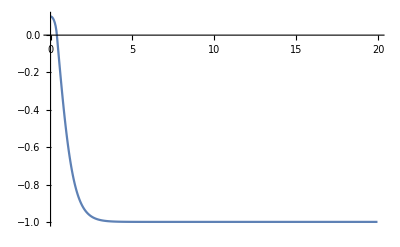

```mathematica
Block[
{rt,rt1,qcrit},
rt[l1_,q1_,r1_]:=NDSolveValue[{2 l^2 r[t]^5-r[t]^7+l^4 r[t]^3 (-1+3 r'[t]^2)-l^6 q (-1+r'[t]^2) √((l^4-2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4-l^2 r[t]^2))+r[t]^4 (l^2 q √((l^4-2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4-l^2 r[t]^2))-l^4 r''[t])+r[t]^2 (-2 l^4 q √((l^4-2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4-l^2 r[t]^2))+l^6 r''[t])==0/.{l->l1,q->q1},r'[0]==0,r[0]==r1},r[t],{t,0.01,20},Method->"BDF"];
rt1[l1_,q1_,r1_,t1_]:=rt[l1,q1,r1]/.{t->t1};
qcrit[l_,rs_]:=rs Sqrt[1-rs^2/l^2];
ListLinePlot[Table[{i,rt1[1,0.1qcrit[1,0.1],0.1,i]//Re},{i,0.01,20,0.05}],PlotRange->All]
]
```

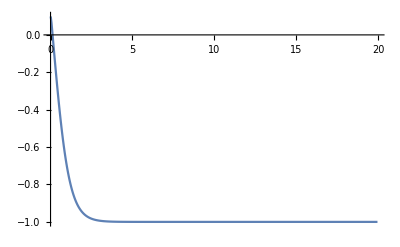

```mathematica
Block[
{rt,rt1,qcrit},
rt[l1_,q1_,r1_]:=NDSolveValue[{2 l^2 r[t]^5-r[t]^7+l^4 r[t]^3 (-1+3 r'[t]^2)-l^6 q (-1+r'[t]^2) √((l^4-2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4-l^2 r[t]^2))+r[t]^4 (l^2 q √((l^4-2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4-l^2 r[t]^2))-l^4 r''[t])+r[t]^2 (-2 l^4 q √((l^4-2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4-l^2 r[t]^2))+l^6 r''[t])==0/.{l->l1,q->q1},r'[0]==0,r[0]==r1},r[t],{t,0.01,20},Method->"BDF"];
rt1[l1_,q1_,r1_,t1_]:=rt[l1,q1,r1]/.{t->t1};
qcrit[l_,rs_]:=rs Sqrt[1-rs^2/l^2];
ListLinePlot[Table[{i,rt1[1,3qcrit[1,0.1],0.1,i]//Re},{i,0.01,20,0.05}],PlotRange->All]
]
```

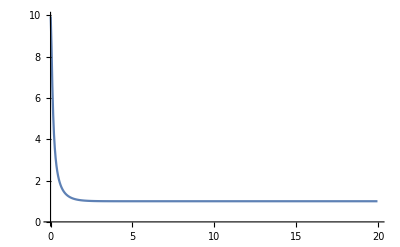

```mathematica
Block[
{rt,rt1,qcrit},
rt[l1_,q1_,r1_]:=NDSolveValue[{2 l^2 r[t]^5-r[t]^7+l^4 r[t]^3 (-1+3 r'[t]^2)-l^6 q (-1+r'[t]^2) √((l^4-2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4-l^2 r[t]^2))+r[t]^4 (l^2 q √((l^4-2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4-l^2 r[t]^2))-l^4 r''[t])+r[t]^2 (-2 l^4 q √((l^4-2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4-l^2 r[t]^2))+l^6 r''[t])==0/.{l->l1,q->q1},r'[0]==0,r[0]==r1},r[t],{t,0.01,20},Method->"BDF"];
rt1[l1_,q1_,r1_,t1_]:=rt[l1,q1,r1]/.{t->t1};
qcrit[l_,rs_]:=rs Sqrt[1-rs^2/l^2];
ListLinePlot[Table[{i,rt1[1,0.1qcrit[1,10],10,i]//Re},{i,0.01,20,0.05}],PlotRange->All]
]
```

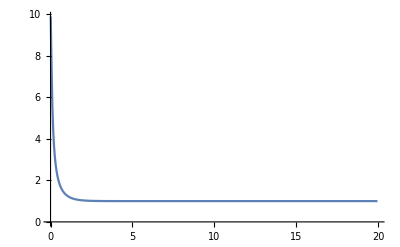

```mathematica
Block[
{rt,rt1,qcrit},
rt[l1_,q1_,r1_]:=NDSolveValue[{2 l^2 r[t]^5-r[t]^7+l^4 r[t]^3 (-1+3 r'[t]^2)-l^6 q (-1+r'[t]^2) √((l^4-2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4-l^2 r[t]^2))+r[t]^4 (l^2 q √((l^4-2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4-l^2 r[t]^2))-l^4 r''[t])+r[t]^2 (-2 l^4 q √((l^4-2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4-l^2 r[t]^2))+l^6 r''[t])==0/.{l->l1,q->q1},r'[0]==0,r[0]==r1},r[t],{t,0.01,20},Method->"BDF"];
rt1[l1_,q1_,r1_,t1_]:=rt[l1,q1,r1]/.{t->t1};
qcrit[l_,rs_]:=rs Sqrt[1-rs^2/l^2];
ListLinePlot[Table[{i,rt1[1,1.5qcrit[1,10],10,i]//Re},{i,0.01,20,0.05}],PlotRange->All]
]
```